```mathematica
Limit[Exp[-1/x],x->0]
```

Indeterminate

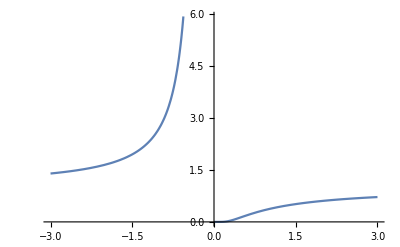

```mathematica
Plot[Exp[-1/T],{T,-3,3}]
```

```mathematica
p=1/(1+Exp[-beta]){{c0^2,c0*Conjugate[c1]},{Conjugate[c0]*c1,c1^2+Exp[-beta]}}
pid={{c0^2,c0*Conjugate[c1]},{Conjugate[c0]*c1,c1^2}}
FullSimplify[Trace[MatrixPower[MatrixPower[p,1/2].pid.MatrixPower[p,1/2],1/2]]]
```

{{c0^2/(1+ⅇ^-beta),(c0 Conjugate[c1])/(1+ⅇ^-beta)},{(c1 Conjugate[c0])/(1+ⅇ^-beta),(c1^2+ⅇ^-beta)/(1+ⅇ^-beta)}}

{{c0^2,c0 Conjugate[c1]},{c1 Conjugate[c0],c1^2}}

{{1,4,{{(-(c1 ⅇ^beta Conjugate[c0] √((1+4)/(1+ⅇ^beta)))/(√2 √(8+4 c0 3 Conjugate[c1]))+(c1 2 √1)/(√2 √1)) (1+1)+1,1},1}},3}
 |  |  |  |

```mathematica
Det[p]
Det[pid]
```

(c0^2 ⅇ^-beta)/((1+ⅇ^-beta)^2)

c0^2 c1^2-c0 c1 Conjugate[c0] Conjugate[c1]

```mathematica
Tr[p.pid]
```

c0^4/(1+ⅇ^-beta)+(c1^2 (c1^2+ⅇ^-beta))/(1+ⅇ^-beta)+(2 c0 c1 Conjugate[c0] Conjugate[c1])/(1+ⅇ^-beta)

```mathematica
Clear["Global`*"]
Solve[(1+1/2*Exp[(-5h)/(kB*T)])/(1+Exp[(-5h)/(kB*T)])==0.99,T]
kB=1.3806452*10^-23(*J/K*);
h=6.62607015*10^-34*10^9(*J/GHz*);
Solve[(1+1/2*Exp[(-5h)/(kB*T)])/(1+Exp[(-5h)/(kB*T)])==0.99,T]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→(1.28475 h)/kB}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→0.0616582}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→0.0107449}}

```mathematica
Clear["Global`*"]
Solve[(1+1/2*1/(Exp[(5h)/(kB*T)]-1))/(1+1/(Exp[(5h)/(kB*T)]-1))==0.99,T]
kB=1.3806452*10^-23(*J/K*);
h=6.62607015*10^-34*10^9(*J/GHz*);
Solve[(1+1/2*1/(Exp[(5h)/(kB*T)]-1))/(1+1/(Exp[(5h)/(kB*T)]-1))==0.99,T]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→(1.27811 h)/kB}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→0.0613398}}

```mathematica
15/Log[2]*h/kB
```

1.03858

```mathematica
(1/(1+2*Exp[(-5h)/(kB*T)]+Exp[(-10h)/(kB*T)])(1+Exp[(-5h)/(kB*T)]))/.T->0.062
(1/(1+2*Exp[(-5h)/(kB*T)]+Exp[(-10h)/(kB*T)])(1+Exp[(-5h)/(kB*T)]))/.T->0.061
```

0.979575

0.980807

```mathematica
mu0=4*π*10^-7
r=100*10^-9(*nm*)
mu1=-9.28476*10^-24
(mu0*mu1*mu1)/(4π*r^3)
```

π/2500000

1/10000000

-9.28476×10^-24

8.62068×10^-33

```mathematica
h=6.626*10^-34
8.620676825760002*^-33/h
```

6.626×10^-34

13.0104